## Initialisation

```mathematica
IONS={"06+","07+","08+","09+","10+","11+","12+","13+","14+"};
ZO=<|"06+"->0,"07+"->1,"08+"->2,"09+"->3,"10+"->4,"11+"->5,"12+"->6,"13+"->7,"14+"->8|>;
<<"AMBiT`";
eV=27.211;
WignerDysonDistribution[d_]=ProbabilityDistribution[(π x)/(2 d^2)Exp[-(π x^2)/(4 d^2)],{x,0,∞},Assumptions->{d>0}];
Zoff=-{58.7535, 54.2619, 49.0055,-94.7303,-94.5785,-93.7886,-92.3306,-90.1759,-87.2972};(*Energy offset from the 4 s^2 4 p^6 4 d^m shell in a.u. from AMBiT*) 

(*Turn off Fit Errors*)
Off[FindFit::cvmit]
Off[NonlinearModelFit::cvmit]
Off[Power::infy]
```

## Image Properties

```mathematica
FS=14; FF="Helvetica"; (* Plotting Font Size and Font*)
ImRes=300; (* Export Image Resolution dpi *)
```

## Choose matrix file

```mathematica
FILE1="C:\\Users\\mattb\\Documents\\Mathematica\\Try_3\\Sn13+_2\\Raw_Data\\9_excitation\\Sn13+_39_0.1o.matrix"
```

C:\Users\mattb\Documents\Mathematica\Try_3\Sn13+_2\Raw_Data\9_excitation\Sn13+_39_0.1o.matrix

## Plots

### Plot Energy Spectra

```mathematica
H1=AmbitReadHamiltonian[FILE1]; (*in a.u. *)
H1=H1 eV;
L1=Length[H1];

(* Get Eigenvalues and vectors*)
ordering1=Ordering[Diagonal[H1]]; (*order diagonals in ascending order*)
H1=(H1ᵀ[[ordering1]])ᵀ[[ordering1]];
EIG1=Eigensystem[H1];
Hii1=Diagonal[H1]-Min[EIG1[[1]]]; (*Diagonal Hamiltonian Elements*)(* in eV*)


(*values*)
Ei1=EIG1[[1]]-Min[EIG1[[1]]](*ZeroOffset1*); 
ORD=True;
If[ORD==True,Ei1=Ei1[[Ordering[Ei1]]]];

 (* vector *)
Cj1=Table[EIG1[[2]][[index]],{index,1,L1,1}];

offDiag1=Flatten[Table[Take[H1[[i,i+1;;-1] ]],{i,1,L1-1}]]; 
V21=Mean[offDiag1^2]
V1=Sqrt[V21];
Hij01=Count[offDiag1,u_/;Abs[u]<10^-6]/Length[offDiag1]//N;
ClearAll[H1,EIG1];
```

0.0623122

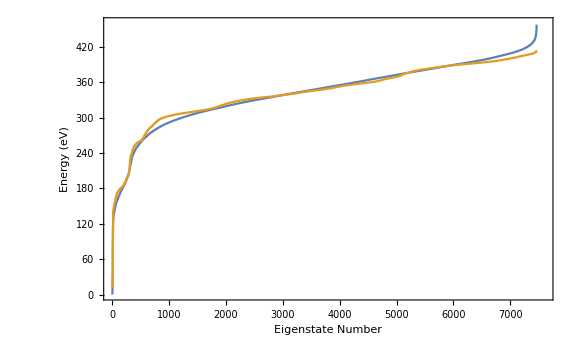

```mathematica
im1=ListLinePlot[{Ei1,Hii1 }(*,PlotLegends->{"Ei1","Hii1"}*)];
s1=Show[im1,ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,PlotRange->{{0,7600},{0,460}},FrameLabel->{"Eigenstate Number","Energy (eV)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF](*,PlotLabel->"Base"*)]
```

```mathematica
Export["C:/Users/mattb/Documents/Mathematica/Try_3/Energies.eps",s1,ImageResolution->ImRes];
```

### Plot Energy Spacing

```mathematica
(* Wigner-Dyson stats*)
Espacing1=Ei1[[2;;-1]]-Ei1[[1;;-2]];(*Energy level spacings*)

(* Ignore the last 10% of values due to large jumps*)
Q1=Quantile[Espacing1,0.9];
pos1=Position[Espacing1,_?(#≤Q1&)];
Espacing21=Extract[Espacing1,pos1];

EHist1=HistogramList[Espacing21];
EBins1=EHist1[[1]];
EVals1=EHist1[[2]];
EBinsMid1=(EBins1[[1;;-2]]+EBins1[[2;;-1]])/2;
ESdata1=Partition[Riffle[EBinsMid1,EVals1],2];

Hspacing1=Hii1[[2;;-1]]-Hii1[[1;;-2]];(*Energy level spacings*)
(*Hspacing1=Hspacing1 eV;(*convert to eV*)*)

(*fits spacing to WD distribution starting at dd=0.001*)
WDfitparams1=NonlinearModelFit[ESdata1,{norm(π x)/(2 d^2)Exp[-(π x^2)/(4 d^2)],d>0},{{d,0.1},{norm,1}},x,ConfidenceLevel->.95];
WDfitval1=WDfitparams1["BestFitParameters"]
ConfInt1=WDfitparams1["ParameterConfidenceIntervals"];
σ951=(ConfInt1[[1]][[2]]-ConfInt1[[1]][[1]])/2;
(* Find Standard error on dd *)

(* Plot Histogram*)

BinSpacing1=Median[Espacing1]/6;
im21=Histogram[{Hspacing1,Espacing1},{BinSpacing1},"PDF"];
im31=Plot[(π x)/(2 d^2)Exp[-(π x^2)/(4 d^2)]/.WDfitval1,{x,0,Max[Espacing1]},PlotStyle->{Black},PlotRange->Full,PlotPoints->1000];
d11=σ951+d/.WDfitval1;
d21=-σ951+d/.WDfitval1;
im311=Plot[(π x)/(2 d11^2)Exp[-(π x^2)/(4 d11^2)],{x,0,Max[Espacing1]},PlotPoints->1000,PlotStyle->{Dashed,Black},PlotRange->Full];
im321=Plot[(π x)/(2 d21^2)Exp[-(π x^2)/(4 d21^2)],{x,0,Max[Espacing1]},PlotPoints->1000,PlotStyle->{Dashed,Black},PlotRange->Full];
s21=Show[{im21,im31,im311,im321},ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,PlotRange->{{0,3d/.WDfitval1},Full},FrameLabel->{"Level Spacing (eV)","Probability"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}]
G=2π V21/d/.WDfitval1
```

```mathematica
Export["C:/Users/mattb/Documents/Mathematica/Try_3/Sn13NNS.eps",s21,ImageResolution->ImRes];
```

### Plot Coefficients - Must run previous 2 sections

```mathematica
nW=0.025L1 d/.WDfitval1 (* Each bin has ~1% of lines *);
Ej=HistogramList[Ei1,{nW}];
EjPos=Prepend[Accumulate[Ej[[2]]],0];(*Cummulative position of index for energy bins*)
Cj2=Cj1^2;


Cj2=Table[Total[#[[EjPos[[i]]+1;;EjPos[[i+1]]]](*ith Ck2 vector*)](*sum of vector components*),{i,1,Length[EjPos]-1}]&/@Cj2; (*put in table*)
EjBins=Ej[[1]] //N;

BinsWidth=EjBins[[2]]-EjBins[[1]]; 
(* Find middle of bins for fitting *)
EjBinsMid=(EjBins[[1;;-2]]+EjBins[[2;;-1]])/2;
(*Normalise Cj*)
CjSquaredBinned=Cj2 /(BinsWidth)//N;
L1 BinsWidth//Print
L1 //Print
BinsWidth//Print
(* Iterate thorugh all eigenvectors *)
Params=ConstantArray[{},L1];
GoF=ConstantArray[{},L1];
Print["Number of Vectors: ",L1]
Print["Progress Bar"]
{Slider[Dynamic[m],{1,L1}],Dynamic[m]}
```

26569.7

7464

3.55972

Number of Vectors: 7464

Progress Bar

{,}

```mathematica
START=1;
END=L1;


For[m=START,m≤END,m++,{
ord=Ordering[CjSquaredBinned[[m]],-1];
Em=EjBins[[ord[[1]]]]; (*Maximum Bin*)
data=Partition[Riffle[EjBinsMid,CjSquaredBinned[[m]]],2];
(*Print[data]*)
fitparams=NonlinearModelFit[data,(2Ds)/(π Γ)(Γ^2/4)/((Ec-x)^2+Γ^2/4),{{Ds,0.001},{Ec,Em},{Γ,0.5}},x];
(*fitparams=NonlinearModelFit[data,2/(π Γ)(Γ^2/4)/((Ec-x)^2+Γ^2/4),{{Ec,Em},{Γ,0.5}},x];*)
fitval=fitparams["BestFitParameters"];
Params[[m]]=fitval;
RMS=RootMeanSquare[fitparams["FitResiduals"]];
R2=fitparams["RSquared"];
GoF[[m]]={RMS,R2};
}];
```

2200

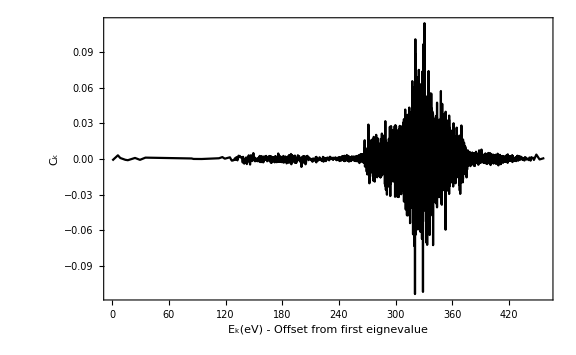

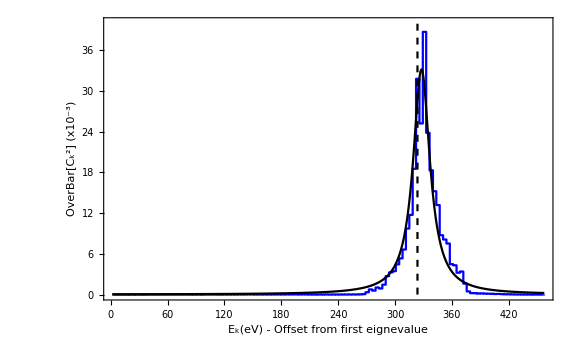

0.280921

21.5896

323.628

```mathematica
m=2200
(*Manipulate[{*)
im4=ListPlot[Partition[Riffle[Ei1,Cj1[[m]]],2],(*PlotRange->{{180,300},{-0.1,0.1}},*)Joined->True,PlotStyle->Black,PlotRange ->{Full,{-Max[Abs[Cj1[[m]]]],Max[Abs[Cj1[[m]]]]}}];

xlabel="E_k (eV) - Offset from first eignevalue";
s3=Show[im4,ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{xlabel,"C_k"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF]]
im5=ListLinePlot[Partition[Riffle[EjBinsMid ,10^3 CjSquaredBinned[[m]]],2],InterpolationOrder->0,PlotStyle->Blue,PlotRange->{{0,EjBinsMid[[-1]]},Full}];
im6=Plot[10^3(2Ds)/(π Γ)(Γ^2/4)/((Ec-x)^2+Γ^2/4)/.Params[[m]],{x,EjBinsMid[[1]],EjBinsMid[[-1]]},PlotStyle->Black,PlotRange->{{0,EjBinsMid[[-1]]},Full}];
(*im6=Plot[10^6 2/(π Γ)(Γ^2/4)/((Ec-x)^2+Γ^2/4)/.Params[[m]],{x,EjBinsMid[[1]],EjBinsMid[[-1]]},PlotStyle->Black,PlotRange->{{0,EjBinsMid[[-1]]},Full}];*)
im7=ListLinePlot[{{Ei1[[m]],0},{Ei1[[m]],40}},PlotStyle->{Dashed,Black}];
s4=Show[{im5,im6,im7},PlotRange->{Automatic,Full},ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{xlabel,"OverBar[C_k^2]  (x10^-3)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF](*,PlotLabel->"Γ = "<> ToString[Γ/.Params[[m]]]<>(*" | D = "<> ToString[Ds/.Params[[m]]]<>*)" | E_c = "<> ToString[Ec/.Params[[m]]]<>"\n R^2 = "<> ToString[GoF[[m]][[2]]]<>" | RMS = "<> ToString[GoF[[m]][[1]] 10^6]<>" x10^-6"*)]
(*},{m,START,END,1}]*)
(*DD=Ds/.Params[[m]];
DD eV//Print*)
Total[CjSquaredBinned[[m]]]
Γ/.Params[[m]]
Ei1[[m]]
```

```mathematica
Export["C:/Users/mattb/Documents/Mathematica/Try_3/Sn13Coeff1.eps",s3,ImageResolution->ImRes];
Export["C:/Users/mattb/Documents/Mathematica/Try_3/Sn13Coeff2.eps",s4,ImageResolution->ImRes];
```